```mathematica
Integrate[Log[u]/u*(Exp[I t u] -1),{u,1,0}]
```

```mathematica
ⅈ t HypergeometricPFQ[{1,1,1},{2,2,2},ⅈ t]I
```

```mathematica
Integrate[Exp[I t Exp[-r]]-1,{r,0,∞}]
```

-EulerGamma+CosIntegral[t]-Log[t]+ⅈ SinIntegral[t]

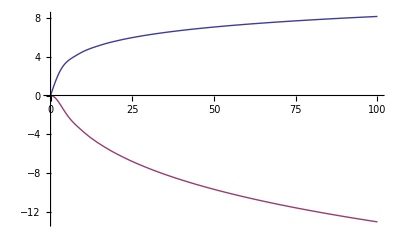

```mathematica
Plot[{Im[I t HypergeometricPFQ[{1,1,1},{2,2,2},I t]],Re[I t HypergeometricPFQ[{1,1,1},{2,2,2},I t]]},{t,0,100}]
```

```mathematica
Integrate[Log[u],{u,0,a}]
```

a (-1+Log[a])

```mathematica
Integrate[Log[u],u]
```

-u+u Log[u]

```mathematica
Integrate[1/r/(10+Log[r]),{r,1,0}]
```

Integrate::idiv: Integral of 1/10 r + r Log[r] does not converge on {0, 1}.

∫_1^0 1/(r (10+Log[r]))ⅆr

```mathematica
Integrate[Log[u]/u*(Exp[I t u]-1),{u,1,0}]
```

ⅈ t HypergeometricPFQ[{1,1,1},{2,2,2},ⅈ t]

```mathematica
Integrate[Cos[r^2],{r,0,∞}]
```

(√(π/2))/2

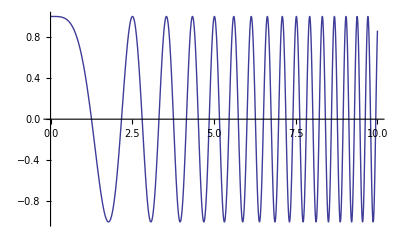

```mathematica
Plot[Cos[r^2],{r,0,10}]
```

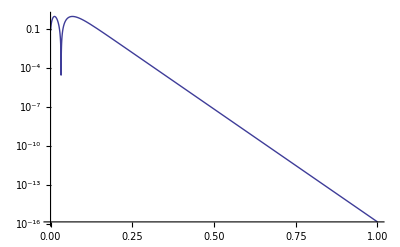

```mathematica
LogPlot[Sin[6*Exp[-20 r]]^2,{r,0,1}]
```

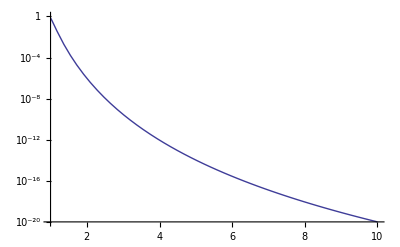

```mathematica
LogPlot[Sin[x^-10]^2 ,{x,1,10}]
```

```mathematica
Series[Sin[x]^2,{x,a,2}]
```

Sin[a]^2+2 Cos[a] Sin[a] (x-a)+(Cos[a]^2-Sin[a]^2) (x-a)^2+O[x-a]^3

```mathematica
f[x_]:=Evaluate[Series[Sin[t/2*x]^2,{x,1,2}]//Simplify]
```

```mathematica
f[y^-a]
```

SeriesData::sdatv: First argument y^-a is not a valid variable.

Sin[t/2]^2+1/2 t Sin[t] (y^-a-1)+1/4 t^2 Cos[t] (y^-a-1)^2+O[y^-a-1]^3

```mathematica
ISin[t/2]^2+1/2 t Sin[t] (y^-a-1)
```

```mathematica
Integrate[Sin[y^-a]^2/.a-> 20,{y,1,∞}]
```

1/4 (-2+2 Cos[2]+2 ⅈ ExpIntegralE[1/20,-2 ⅈ]-2 ⅈ ExpIntegralE[1/20,2 ⅈ]-(-1)^(1/40) 2^(1/20) (-1+(-1)^(19/20)) Gamma[19/20])

```mathematica
3
```

```mathematica
Series[x^-5,{x,1,10}]
```

1-5 (x-1)+15 (x-1)^2-35 (x-1)^3+70 (x-1)^4-126 (x-1)^5+210 (x-1)^6-330 (x-1)^7+495 (x-1)^8-715 (x-1)^9+1001 (x-1)^10+O[x-1]^11

```mathematica
Integrate[Sin[t u/2]^2/u,{u,1,0}]//Simplify
Integrate[Sin[t u]/u,{u,1,0}]//Simplify
```

1/2 (-EulerGamma+CosIntegral[t]-Log[t])

-SinIntegral[t]

```mathematica
Integrate[Log[u] Sin[t u/2]^2/u,{u,1,0}]//Simplify
Integrate[Log[u] Sin[t u]/u,{u,1,0}]//Simplify
```

1/16 t^2 HypergeometricPFQ[{1,1,1},{3/2,2,2,2},-t^2/4]

1/27 t^3 HypergeometricPFQ[{3/2,3/2},{5/2,5/2,5/2},-t^2/4]+SinIntegral[t]

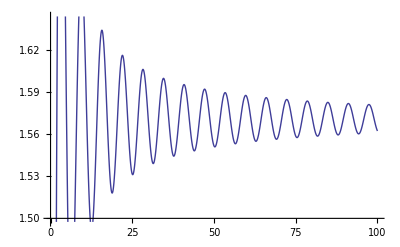

```mathematica
Plot[SinIntegral[t],{t,0,100}]
```

```mathematica
Integrate[Sin[t u/2]^2/u^(3/2),{u,∞,0}]//Simplify
Integrate[Sin[t u]/u^(3/2),{u,∞,0}]//Simplify
```

If[Abs[Im[t]]==0,-√(π/2) (t^2)^(1/4),Integrate[Sin[(u t)/2]^2/u^(3/2),{u,0,∞},Assumptions→Abs[Im[t]]≠0]]

If[Abs[Im[t]]==0,-(√(2 π) (t^2)^(3/4))/t,Integrate[Sin[u t]/u^(3/2),{u,0,∞},Assumptions→Abs[Im[t]]≠0]]

```mathematica
Integrate[Sin[t u/2]^2/u^(2),{u,∞,0}]//Simplify
Integrate[Sin[t u]/u^(2),{u,∞,0}]//Simplify
```

If[t∈Reals,-1/4 π Abs[t],Integrate[Sin[(u t)/2]^2/u^2,{u,0,∞},Assumptions→t∉Reals]]

Integrate::idiv: Integral of Sin[t u]/u^2 does not converge on {0, ∞}.

∫_∞^0 Sin[t u]/u^2 ⅆu

```mathematica
Integrate[Sin[t u/2]^2/u^(8/6),{u,∞,0}]//Simplify
Integrate[Sin[t u]/u^(8/6),{u,∞,0}]//Simplify
```

If[Abs[Im[t]]==0,-3/4 ((-ⅈ t)^(1/3)+(ⅈ t)^(1/3)) Gamma[2/3],Integrate[Sin[(u t)/2]^2/u^(4/3),{u,0,∞},Assumptions→Abs[Im[t]]≠0]]

If[Abs[Im[t]]==0,-3/2 ⅈ ((-ⅈ t)^(1/3)-(ⅈ t)^(1/3)) Gamma[2/3],Integrate[Sin[u t]/u^(4/3),{u,0,∞},Assumptions→Abs[Im[t]]≠0]]

```mathematica
Integrate[Sin[t u/2]^2/u^(7/5),{u,∞,0}]//Simplify
Integrate[Sin[t u]/u^(7/5),{u,∞,0}]//Simplify
```

If[Abs[Im[t]]==0,-5/8 ((-ⅈ t)^(2/5)+(ⅈ t)^(2/5)) Gamma[3/5],Integrate[Sin[(u t)/2]^2/u^(7/5),{u,0,∞},Assumptions→Abs[Im[t]]≠0]]

If[Abs[Im[t]]==0,-5/4 ⅈ ((-ⅈ t)^(2/5)-(ⅈ t)^(2/5)) Gamma[3/5],Integrate[Sin[u t]/u^(7/5),{u,0,∞},Assumptions→Abs[Im[t]]≠0]]